```mathematica
n=2; (*Število členov*)

Linspace[a_,b_,n_Integer?Positive]:=If[n==1,{a},Table[a+(b-a)*(i-1)/(n-1),{i,n}]];

Midspace[a_,b_,n_Integer?Positive]:=Module[{pts},pts=Linspace[a,b,n];
Most[pts]+Differences[pts]/2];(*bo uporabno kasneje*)

(*B*)
B=DiagonalMatrix[ConstantArray[-3,n]]+DiagonalMatrix[ConstantArray[1,n-1],1]+DiagonalMatrix[ConstantArray[1,n-1],-1];
B[[1,1]]=-2;
B[[n,n]]=-2;
MatrixForm[B]

(*X*)

X=ArrayFlatten[{{ConstantArray[0,{n,n}],IdentityMatrix[n]},{k*B,-γ*IdentityMatrix[n]}}];
MatrixForm[X]

(*Y*)
T=ConstantArray[0,{n,n}];
T[[1,1]]=L;
T[[n,n]]=R;
Y=ArrayFlatten[{{ConstantArray[0,{n,n}],ConstantArray[0,{n,n}]},{ConstantArray[0,{n,n}],4 γ*T}}];
MatrixForm[Y]

(*Diagonalize*)
{vals,vects}=Eigensystem[X];
E=DiagonalMatrix[vals];
V=Transpose@vects;
Vi=Inverse[V];

(*Č*)
K=Vi.Y.Transpose[Vi];
Č=Table[-K[[i,j]]/(vals[[i]]+vals[[j]]),{i,2*n},{j,2*n}];

C0=Simplify[V.Č.Transpose[V]];

MatrixForm[C0]
TeXForm[C0];
```

(-2 | 1
1 | -2)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-2 k | k | -γ | 0
k | -2 k | 0 | -γ)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 4 L γ | 0
0 | 0 | 0 | 4 R γ)

Set::wrsym: Symbol ⅇ is Protected.

((2 k (L+R)+(7 L+R) γ^2)/(3 k (k+2 γ^2)) | (L+R)/(3 k) | 0 | ((L-R) γ)/(k+2 γ^2)
(L+R)/(3 k) | (2 k (L+R)+(L+7 R) γ^2)/(3 k (k+2 γ^2)) | ((-L+R) γ)/(k+2 γ^2) | 0
0 | ((-L+R) γ)/(k+2 γ^2) | (k (L+R)+4 L γ^2)/(k+2 γ^2) | 0
((L-R) γ)/(k+2 γ^2) | 0 | 0 | (k (L+R)+4 R γ^2)/(k+2 γ^2))

```mathematica
3
```

3

```mathematica
TeXForm[C0]
```

\left(
\begin{array}{cccc}
 \frac{2 k (L+R)+\gamma ^2 (7 L+R)}{3 k \left(2 \gamma ^2+k\right)} & \frac{L+R}{3
   k} & 0 & \frac{\gamma  (L-R)}{2 \gamma ^2+k} \\
 \frac{L+R}{3 k} & \frac{2 k (L+R)+\gamma ^2 (L+7 R)}{3 k \left(2 \gamma
   ^2+k\right)} & \frac{\gamma  (R-L)}{2 \gamma ^2+k} & 0 \\
 0 & \frac{\gamma  (R-L)}{2 \gamma ^2+k} & \frac{k (L+R)+4 \gamma ^2 L}{2 \gamma
   ^2+k} & 0 \\
 \frac{\gamma  (L-R)}{2 \gamma ^2+k} & 0 & 0 & \frac{k (L+R)+4 \gamma ^2 R}{2
   \gamma ^2+k} \\
\end{array}
\right)

{(k (L+R)+4 L γ^2)/(2 (k+2 γ^2)),(k (L+R)+4 R γ^2)/(2 (k+2 γ^2))}

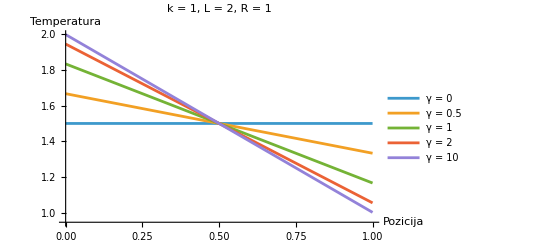

gammas2.png

```mathematica
Es = 1/2 *  Diagonal[C0][[n +1;;]]
Js = Table[k*C0[j,n+j+1],{j,0,n-1}];
xs=Subdivide[0,1,n-1];

Es = Transpose[{xs,Es}];
Js = Transpose[{xs,Js}];

(*plot temperature*)
p = ListLinePlot[
{Es /.  {γ -> 0, k -> 1, L ->2, R-> 1},
Es /.  {γ -> 0.5, k -> 1, L ->2, R-> 1},
Es /.  {γ -> 1, k -> 1, L ->2, R-> 1},
Es /.  {γ -> 2, k -> 1, L ->2, R-> 1},
Es /.  {γ -> 10, k -> 1, L ->2, R-> 1}
},
PlotLabel->"k = 1, L = 2, R = 1",
AxesLabel->{"Pozicija", "Temperatura"},
PlotLegends-> {
"γ = 0",
"γ = 0.5",
"γ = 1",
"γ = 2",
"γ = 10"
}

]

Export["gammas"<>ToString[n]<>".png",p]
```

{(k (L+R)+4 L γ^2)/(2 (k+2 γ^2)),(k (L+R)+4 R γ^2)/(2 (k+2 γ^2))}

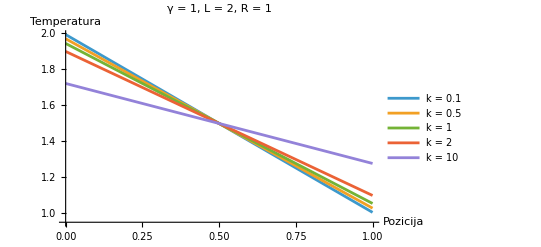

ks2.png

```mathematica
Es = 1/2 *  Diagonal[C0][[n +1;;]]
Js = Table[k*C0[j,n+j+1],{j,0,n-1}];
xs=Subdivide[0,1,n-1];

Es = Transpose[{xs,Es}];
Js = Transpose[{xs,Js}];

(*plot temperature*)
p = ListLinePlot[
{Es /.  {γ -> 2, k -> 0.1, L ->2, R-> 1},
Es /.  {γ -> 2, k -> 0.5, L ->2, R-> 1},
Es /.  {γ -> 2, k -> 1, L ->2, R-> 1},
Es /.  {γ -> 2, k -> 2, L ->2, R-> 1},
Es /.  {γ -> 2, k -> 10, L ->2, R-> 1}
},
PlotLabel->"γ = 1, L = 2, R = 1",
AxesLabel->{"Pozicija", "Temperatura"},
PlotLegends-> {
"k = 0.1",
"k = 0.5",
"k = 1",
"k = 2",
"k = 10"
}

]

Export["ks"<>ToString[n]<>".png",p]
```

```mathematica
Es = 1/2 *  Diagonal[C0][[n +1;;]];
Js = Table[k*C0[[j,n+j+1]],{j,1,n-1}];
xs=Linspace[0,1,n];
xsJ=Midspace[0,1,n];


Es = Transpose[{xs,Es}];
Js = Transpose[{xsJ,Js}];


(*plot temperature*)
p = ListLinePlot[
{Js /.  {γ -> 0, k -> 1, L ->2, R-> 1},Js /.  {γ -> 0.5, k -> 1, L ->2, R-> 1},
Js /.  {γ -> 1, k -> 1, L ->2, R-> 1},
Js /.  {γ -> 2, k -> 1, L ->2, R-> 1},
Js /.  {γ -> 10, k -> 1, L ->2, R-> 1}
},
PlotLabel->"k = 1, L = 2, R = 1",
AxesLabel->{"Pozicija", "Temperatura"},
PlotLegends-> {
"γ = 0",
"γ = 0.5",
"γ = 1",
"γ = 2",
"γ = 10"
}

];

Export["gammasJ"<>ToString[n]<>".png",p]
```

gammasJ2.png

```mathematica
Dimensions[Js]
```

{1,2}

{(k (L-R) γ)/(k+2 γ^2)}

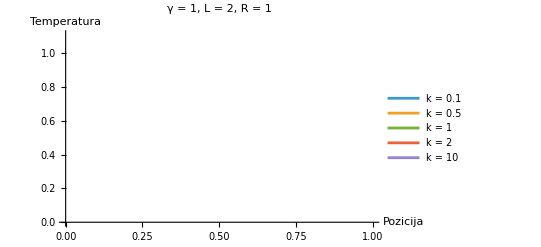

ksJ2.png

```mathematica
Es = 1/2 *  Diagonal[C0][[n +1;;]];
Js = Table[k*C0[[j,n+j+1]],{j,1,n-1}]
xs=Linspace[0,1,n];
xsJ=Midspace[0,1,n];

Es = Transpose[{xs,Es}];
Js = Transpose[{xsJ,Js}];

(*plot temperature*)
p = ListLinePlot[
{Js /.  {γ -> 2, k -> 0.1, L ->2, R-> 1},
Js /.  {γ -> 2, k -> 0.5, L ->2, R-> 1},
Js /.  {γ -> 2, k -> 1, L ->2, R-> 1},
Js /.  {γ -> 2, k -> 2, L ->2, R-> 1},
Js /.  {γ -> 2, k -> 10, L ->2, R-> 1}
},
PlotLabel->"γ = 1, L = 2, R = 1",
AxesLabel->{"Pozicija", "Temperatura"},
PlotLegends-> {
"k = 0.1",
"k = 0.5",
"k = 1",
"k = 2",
"k = 10"
}

]

Export["ksJ"<>ToString[n]<>".png",p]
```